## First

One reason why you might not have extra dips in the graphs is because the pulse length might be too short.



Todo:
- Rabi oscillation function. Just solves the system for a specific frequency.

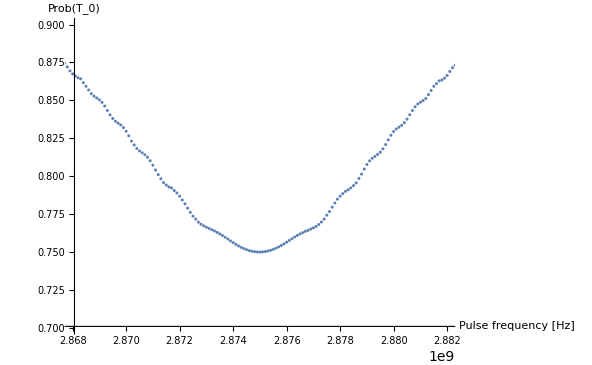
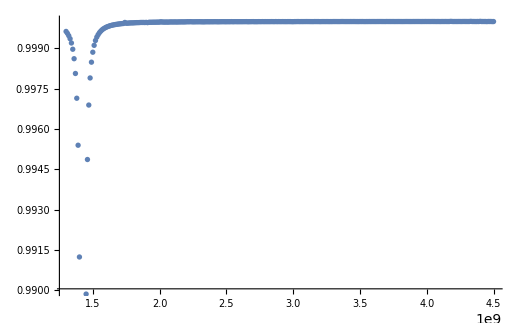
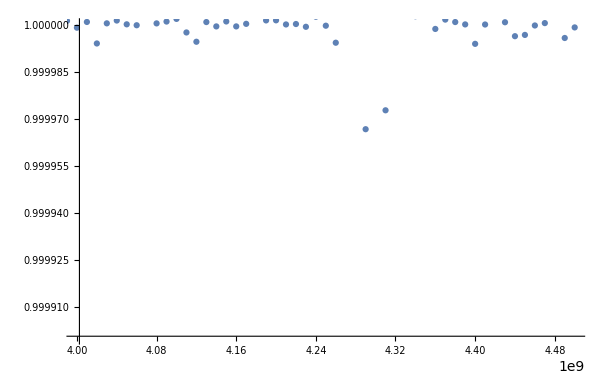
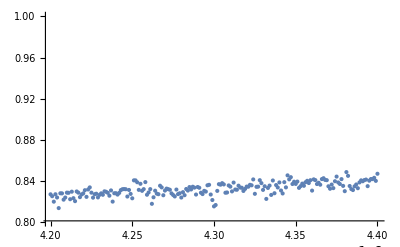
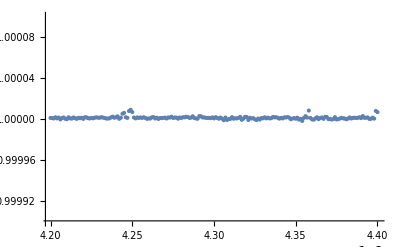
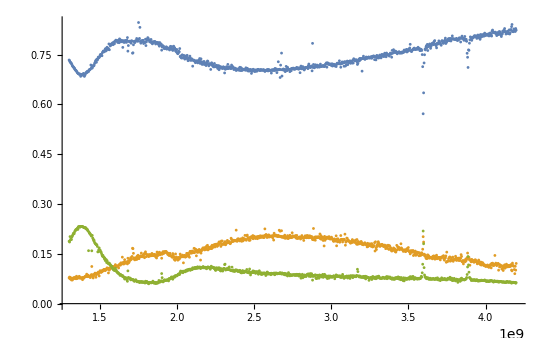
After speaking to Ji-Won, I increased the pulseAmplitude from 7*10^6 to 2.7*10^9 Hz. This is because angular momentum should not necessarily be conserved, as J doesn’t commute with the Hamiltonian at all times, especially during the perturbation itself. Previously, since the pulseAmplitude was fairly low, the angular momentum breaking transitions might’ve been supressed. It might get better now.

I’ve also increased the pulse length from 2 microseconds to 3. I’m wondering whether certain smaller dips might disappear as the shorter frequencies (corresponding to the smaller energy gaps) won’t register on the very short pulses. Also, having larger pulses might also remove those weird oscillations in the probability that I usually observe, around resonance.

-Graphics-

At some point I’ll run the simulation again, but with a density matrix that is an ensemble of the  |0,-1>, |0,0> and |0, 1> states. This should be a reasonable approximation for the experiment. In the experiment, after the initialization we know that ms=0 but not the spin of the nucleus. Although, now that I think about it, this particular density matrix assumes that the true state of the system aren’t mixed. Meaning: after initialisation, the state of the system is not some superposition of  |0,-1>, |0,0> and |0, 1>. Ji-Won said something that might’ve indicated that that was the case.

If that isn’t a valid approximation, I could try to find a way to build a density matrix that assigns equal probability to any superposition of |0,-1>, |0,0> and |0, 1>. How do I do that? That would have to be through some sort of integral I guess. Could it be this?

((∫_0)^1 ⅆ p_1(∫_0)^p_1 ⅆ p_2(∫_0)^(2π)ⅆ θ_1(∫_0)^(2π)ⅆθ_2 [  √p_1|0,1⟩   +  √p_2 e^(i θ_1)|0,0⟩  + √(1 - p_1 - p_2)e^(i θ_2)|0,-1⟩ ])/((2π)^2(∫_0)^1 ⅆ p_1(∫_0)^p_1 ⅆ p_2)

Which is a uniform distribution. I could also try a canonical distribution.

-Graphics-

Might be okay to assume that the system, after the green pulse, is is prepared in some sort of superposition of the |0,-1>, |0,0> and |0, 1> states. In which case we might even get enough dips.

Observations:

The system I’ve been working on now is:

("E" | "|ψ_E⟩" | "⟨J_z⟩"
"---" | "---" | "---"
4.30771×10^9 | {-0.00048692 "|0,-1⟩",1. "|-1,0⟩"} | -1.
4.30508×10^9 | {3.56211×10^-7 "|1,-1⟩",-0.000487796 "|0,0⟩",1. "|-1,1⟩"} | 0.
4.30045×10^9 | {1. "|-1,-1⟩"} | -2.
1.43229×10^9 | {0.999999 "|1,0⟩",-0.00146129 "|0,1⟩"} | 1.
1.42934×10^9 | {0.999999 "|1,-1⟩",-0.0014692 "|0,0⟩",-1.07288×10^-6 "|-1,1⟩"} | 0.
1.42533×10^9 | {1. "|1,1⟩"} | 2.
-4109.7 | {0.0014692 "|1,-1⟩",0.999999 "|0,0⟩",0.000487795 "|-1,1⟩"} | 0.
-4.79524×10^6 | {0.00146129 "|1,0⟩",0.999999 "|0,1⟩"} | 1.
-5.10885×10^6 | {1. "|0,-1⟩",0.00048692 "|-1,0⟩"} | -1.)

This has an applied field of 503G.

I prepared the system in the |1, 1> state, and contrary to what I expected, I got a transition (thus breaking angular momentum conservation).

-Graphics-


The state goes from the |1,1> state to a |0,0> state, at an energy around 1.4 GHz. My guess is that it goes from the 6th to the 7th eigenstate on the spectrum graph, from the top. The surprising thing is that I can’t find a second transition at a higher energy (from the 6th to the 2nd eigenstate). I might’ve found a really small peak though:

-Graphics-

I’ll try that with a higher resolution. Now with a 3ms pulse with amplitude of 2.7 GHz.

-Graphics-

Not what I expected... Trying it again with 7 MHz. Nothing:

-Graphics-

Try again with 2.7 GHz, and over the whole range.

-Graphics-

Interesting. Definitely have some more dips now. Not sure what the middle bit means. 


Will try again but lowering the amplitude to 0.27 GHz. After that, I should investigate the dips at the rightmost end.

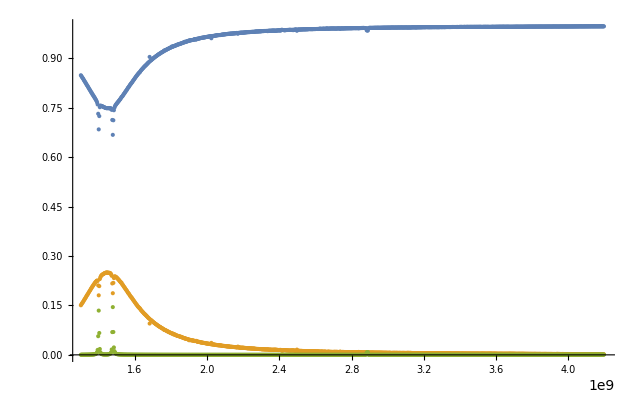
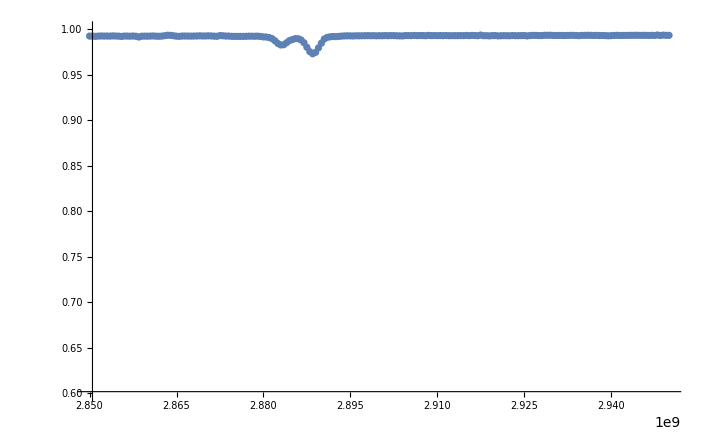
-Graphics-

Very interesting. There does seems to be a small dip at around 2.87 GHz. This would correspond to the transition that I was missing earlier. We’re really getting somewhere now! 

-Graphics-

It’s definitely a dip. We’re getting way more dips now than before.


Now, let’s try with the groundstate again.

#### Run: B0=30G, from ground-state, with a 0.27 GHz pulse

Parameters:

```mathematica
pulseAmplitude = 2.7*10^8; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 1*10^6; (* [Hz] *)
pulseFreqEnd =3.2*10^9; (* [Hz] *) 
pulseFreqStep = 1*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 3*10^-6; (* End-time of NDSolve [s] *)

B0 =30 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)
```

Spectrum:
("E" | "|ψ_E⟩" | "⟨J_z⟩"
"---" | "---" | "---"
2.95408×10^9 | {-0.00070969 "|0,-1⟩",1. "|-1,0⟩"} | -1.
2.9513×10^9 | {8.88529×10^-6 "|1,-1⟩",-0.000711558 "|0,0⟩",1. "|-1,1⟩"} | 0.
2.94696×10^9 | {1. "|-1,-1⟩"} | -2.
2.78592×10^9 | {1. "|1,0⟩",-0.000752455 "|0,1⟩"} | 1.
2.78313×10^9 | {1. "|1,-1⟩",-0.00075454 "|0,0⟩",-9.42219×10^-6 "|-1,1⟩"} | 0.
2.77882×10^9 | {1. "|1,1⟩"} | 2.
-3078.81 | {0.000754547 "|1,-1⟩",0.999999 "|0,0⟩",0.000711551 "|-1,1⟩"} | 0.
-4.94235×10^6 | {0.000752455 "|1,0⟩",1. "|0,1⟩"} | 1.
-4.96072×10^6 | {1. "|0,-1⟩",0.00070969 "|-1,0⟩"} | -1.)

The starting system is the groundstate.

Results:

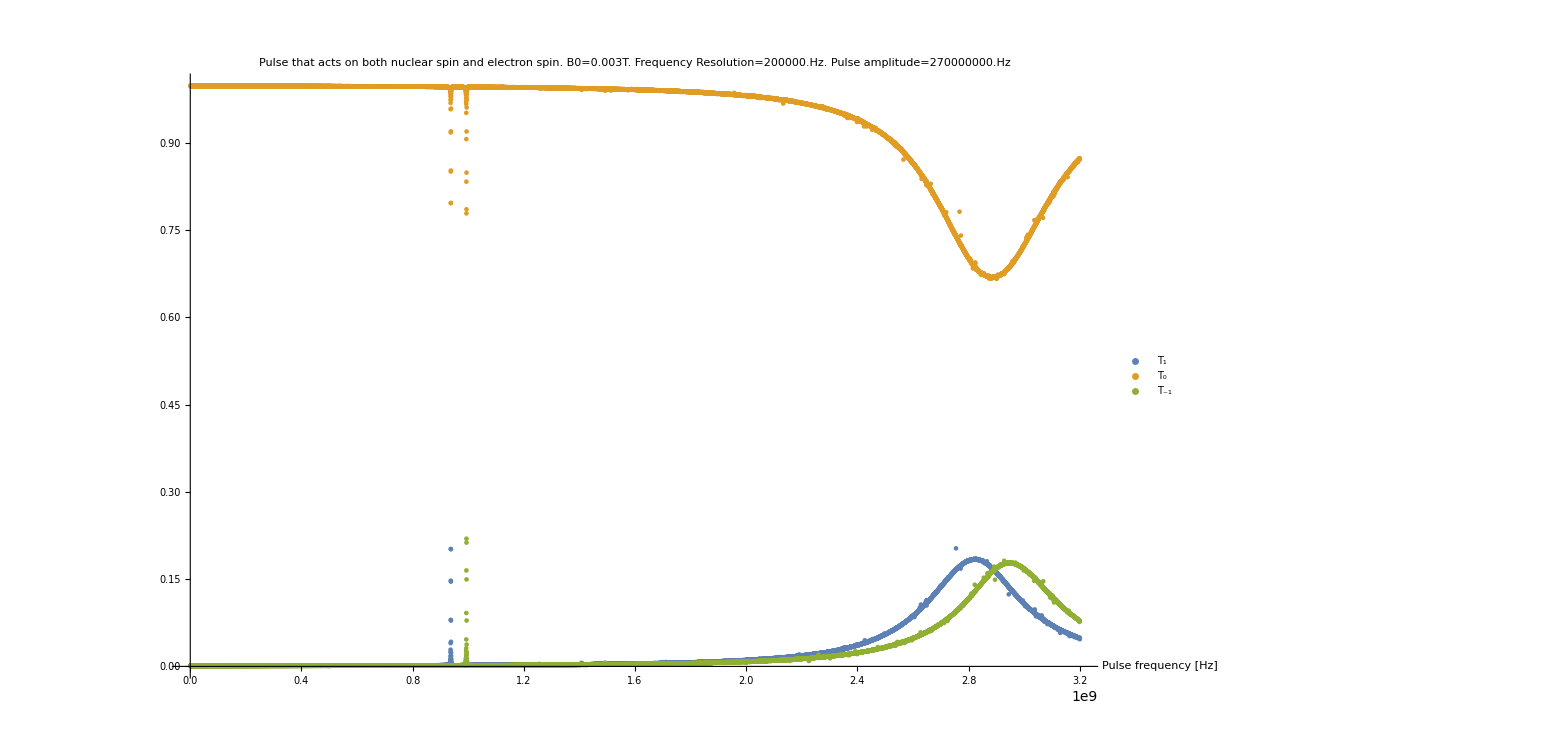

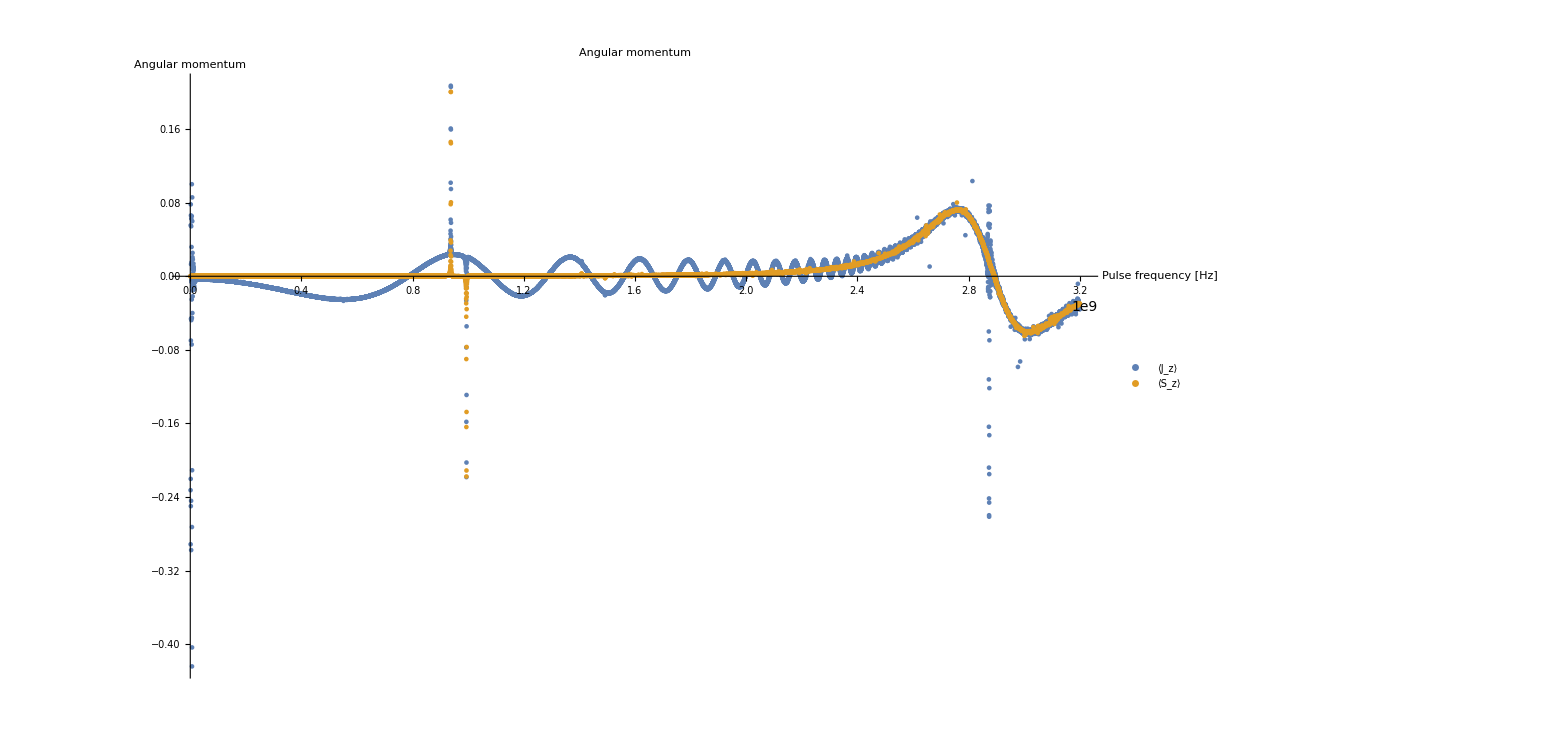

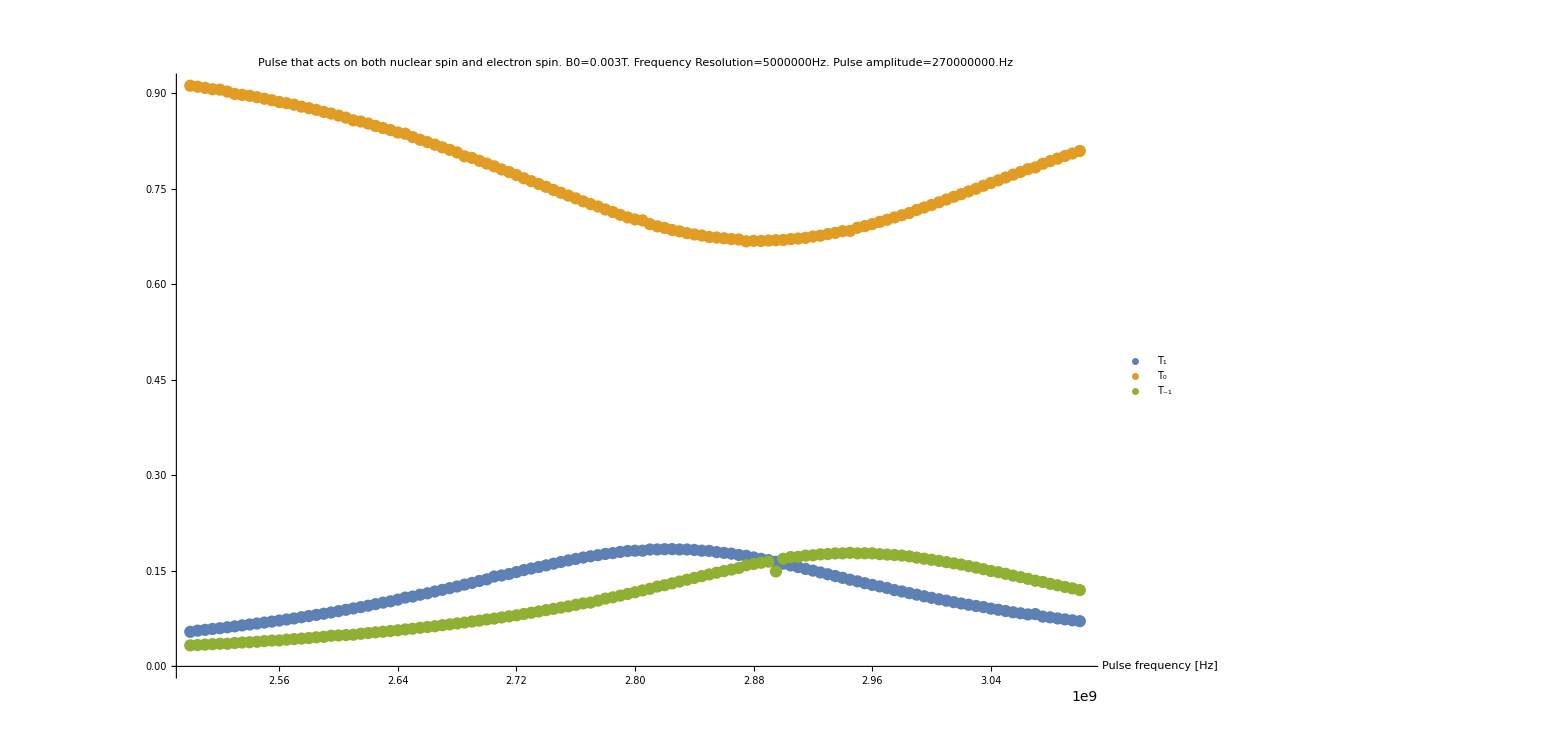

Analysis:

Not sure what to make of the dips on the lower end. They’re about 1GHz and they don’t correspond to anything in the spectrum.

The rightmost dip in the right side of the graph looks like the accumulation of the two peaks by the T_1 and T_-1, these match roughly with the spectrum.

I’ll run the same but now with a 2.7*10^7Hz pulse

## Run: B0=30G, from ground-state, with a 270 MHz pulse

Parameters:

```mathematica
pulseAmplitude = 2.7*10^7; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.6*10^6; (* [Hz] *)
pulseFreqEnd =3.1*10^9; (* [Hz] *) 
pulseFreqStep = 1*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 3*10^-6; (* End-time of NDSolve [s] *)

B0 =30 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)
```

Spectrum:
("E" | "|ψ_E⟩" | "⟨J_z⟩"
"---" | "---" | "---"
2.95408×10^9 | {-0.00070969 "|0,-1⟩",1. "|-1,0⟩"} | -1.
2.9513×10^9 | {8.88529×10^-6 "|1,-1⟩",-0.000711558 "|0,0⟩",1. "|-1,1⟩"} | 0.
2.94696×10^9 | {1. "|-1,-1⟩"} | -2.
2.78592×10^9 | {1. "|1,0⟩",-0.000752455 "|0,1⟩"} | 1.
2.78313×10^9 | {1. "|1,-1⟩",-0.00075454 "|0,0⟩",-9.42219×10^-6 "|-1,1⟩"} | 0.
2.77882×10^9 | {1. "|1,1⟩"} | 2.
-3078.81 | {0.000754547 "|1,-1⟩",0.999999 "|0,0⟩",0.000711551 "|-1,1⟩"} | 0.
-4.94235×10^6 | {0.000752455 "|1,0⟩",1. "|0,1⟩"} | 1.
-4.96072×10^6 | {1. "|0,-1⟩",0.00070969 "|-1,0⟩"} | -1.)

The starting system is the ground-state.

Results:

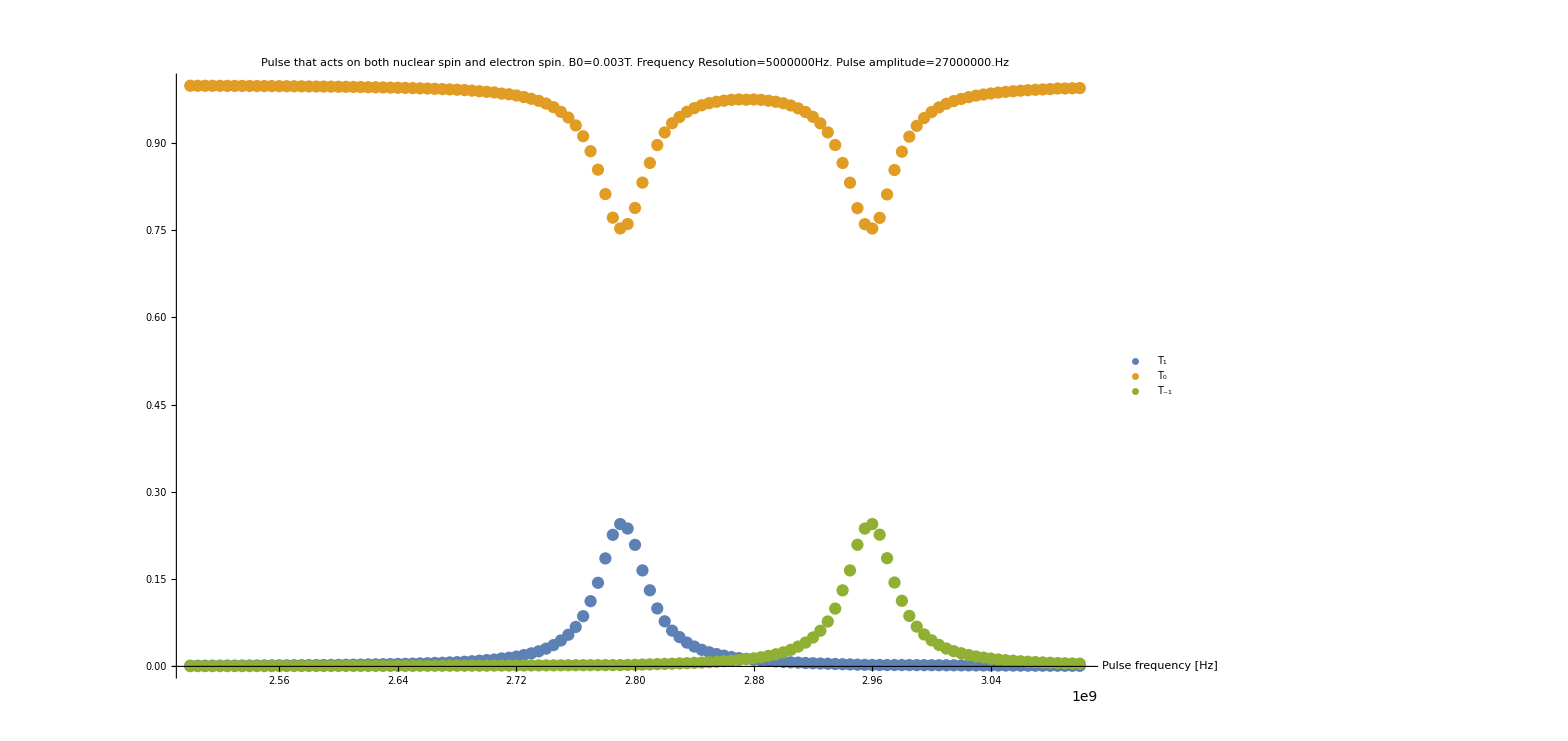

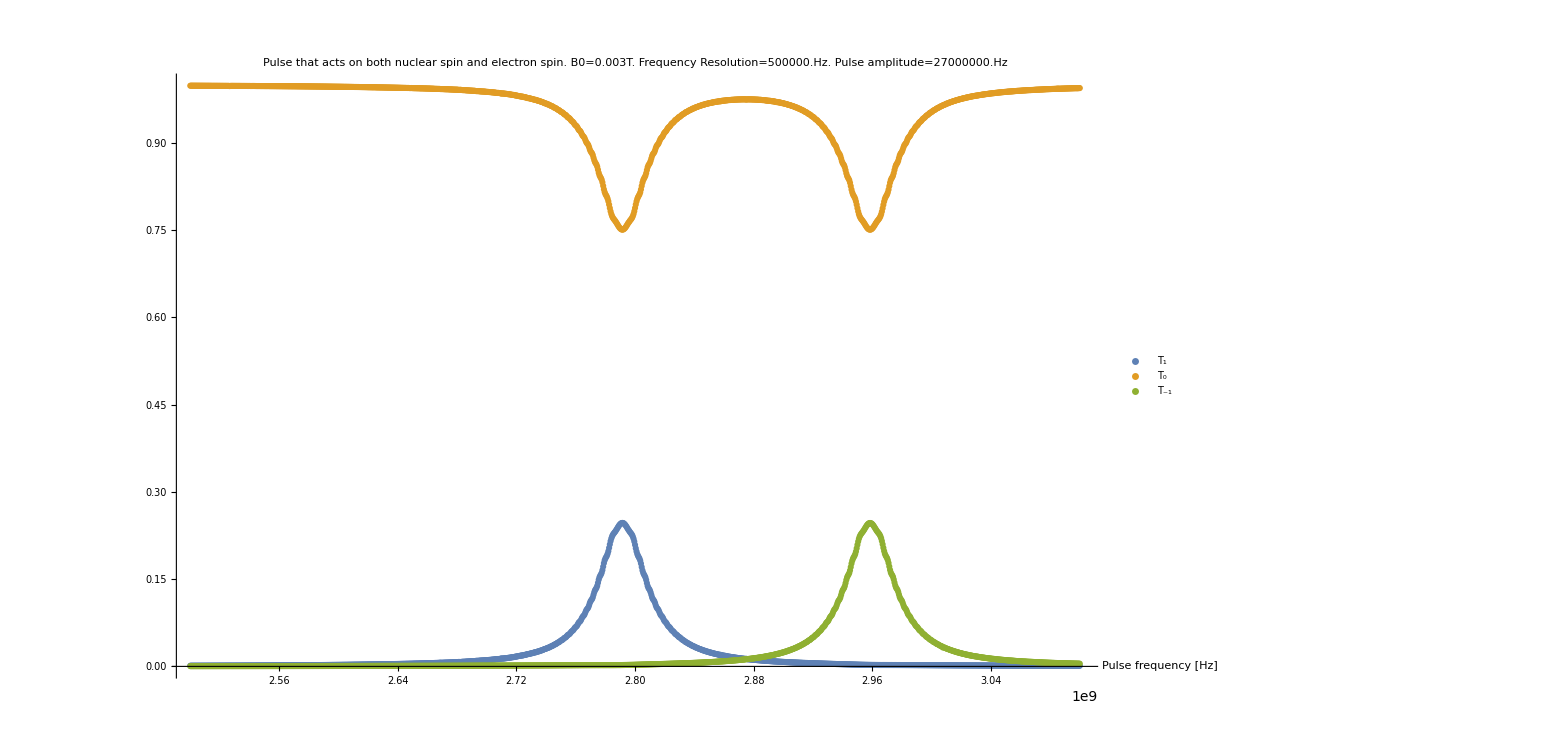
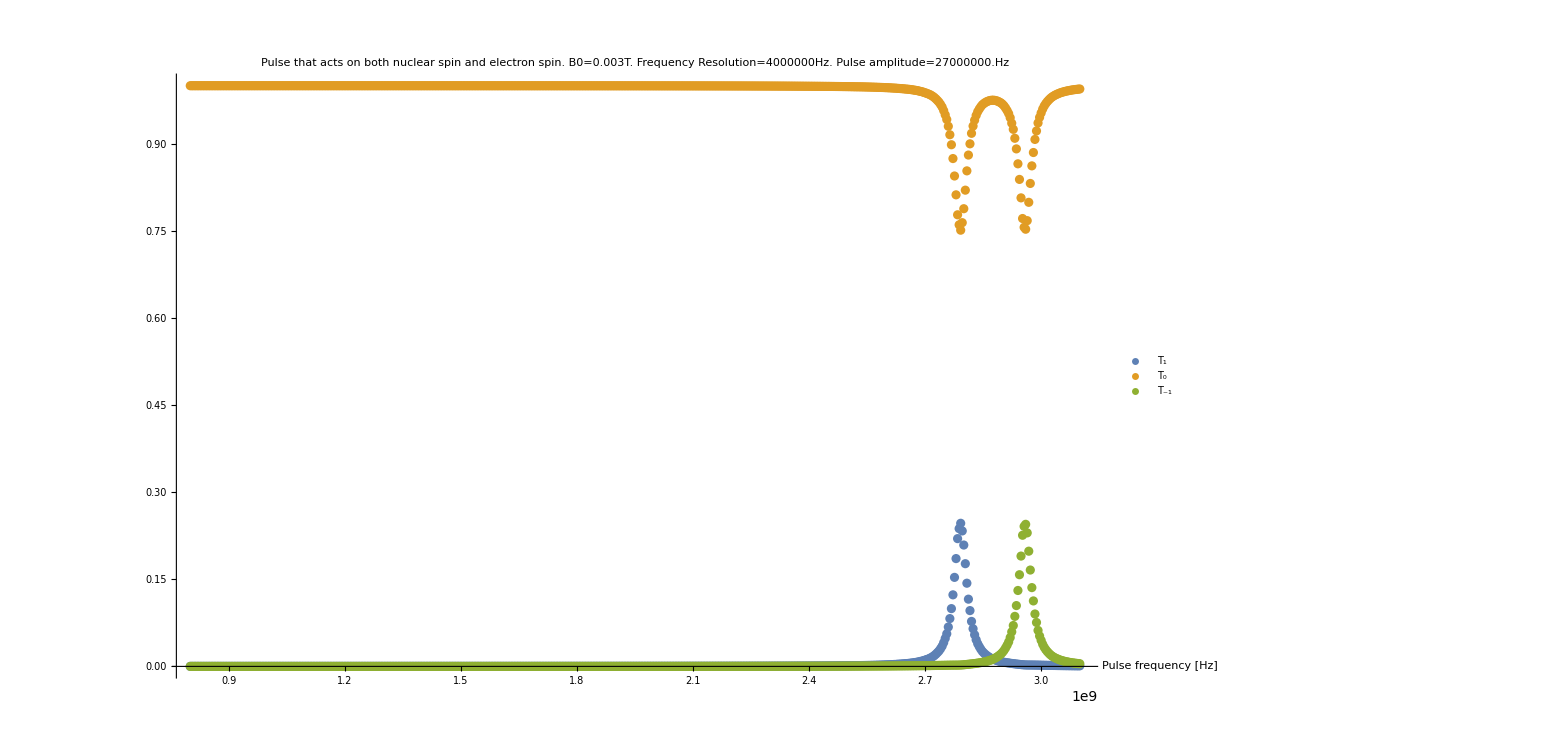
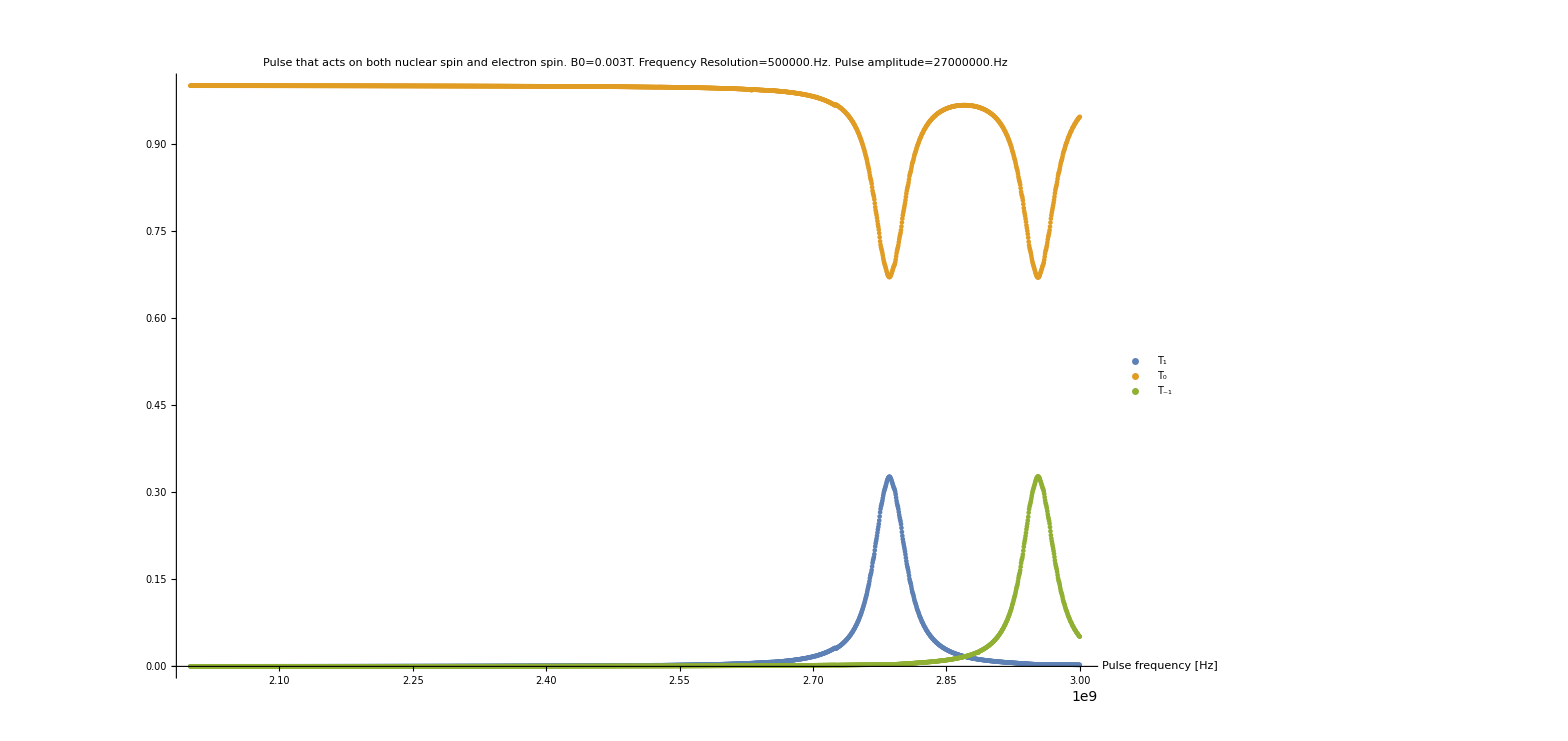
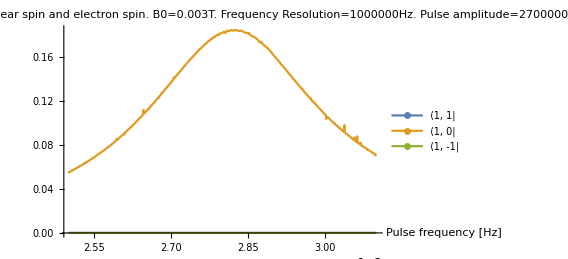
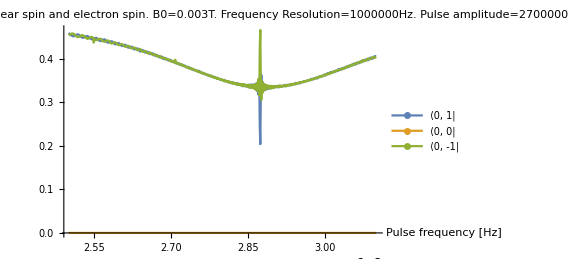
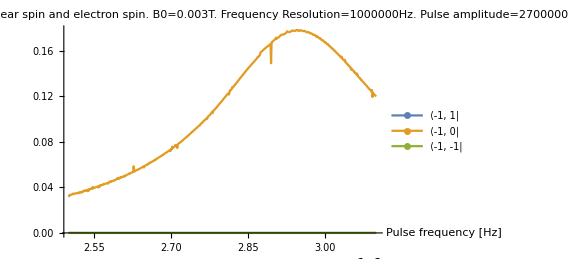
The left peak is at 2.79×10^9, and the right peak is at 2.96×10^9. This matches well. Ideally we’d find six dips in total.

Next, a run with a lower frequency step, to see if there are any additional peaks.

-Graphics-

Doesn’t seem to be any....

Next, a run for the lower frequency ranges.

-Graphics-

So those strange peaks from before are now gone.

Next, lower the amplitude by a a factor of 10, to 27 MHz.

-Graphics-

Not much difference. Running the simulation, but this time checking each of the individual 9 states, we see that actually not only the transitions to the 1,0 and the -1, 0 states actually happen:

-Graphics--Graphics--Graphics-

So it’s not a matter of resolution at least. If the pulse amplitude was really huge, maybe we would see the transitions. But even in that case, the uncertainty of the peak would be too large to see them.

Observations:

- Although a large amplitude is needed for the spin conservation to break, if it’s too large the dips/peaks start to blur together into one. Compare the this run to the one prior.

```mathematica
4.960720222093582*^6 + 2.7859247983677793*^9
```

2.79089×10^9

```mathematica
4.960720222093582*^6 + 2.954078272136635*^9
```

2.95904×10^9

## Run: B0=100G, uniform mixture of T0 states, with a 270 MHz pulse

nv_center_simulation_NO_SPIN_BATH2017-08-22_23.20.49

Prepared the initial state in a uniform mixture of the 0,1   0,0  and  0,-1  states.

### Initialisation

#### Simulation parameters

```mathematica
pulseAmplitude = 2.7*10^8; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 1*10^9; (* [Hz] *)
pulseFreqEnd =4*10^9; (* [Hz] *) 
pulseFreqStep = 0.5*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 7*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 6001

#### Setup Hamiltonian

```mathematica
spins = {1, 1};

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋspinSpin =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋCop =  pulseAmplitude* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1], 2-> SpinMatrixX[1] }, {3, 3} ] ;
ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

#### Energy spectrum of the unperturbed Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV, spins];
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];

eigenStates[0,1] = hamiltonianSpectrum[[1]][[3]][[8]];
eigenStates[0,0] = hamiltonianSpectrum[[1]][[3]][[7]];
eigenStates[0,-1] = hamiltonianSpectrum[[1]][[3]][[9]];

generalState = Sqrt[p1] eigenStates[0,1] + Sqrt[p0] eigenStates[0, 0] + Sqrt[1 - p1-p0] eigenStates[0, -1];
propagator = Outer[Times, generalState, generalState];
density0 = NIntegrate[propagator, {p1, 0, 1}, {p0, 0, 1 - p1}]/NIntegrate[1, {p1, 0, 1}, {p0, 0, 1 - p1}];
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Results

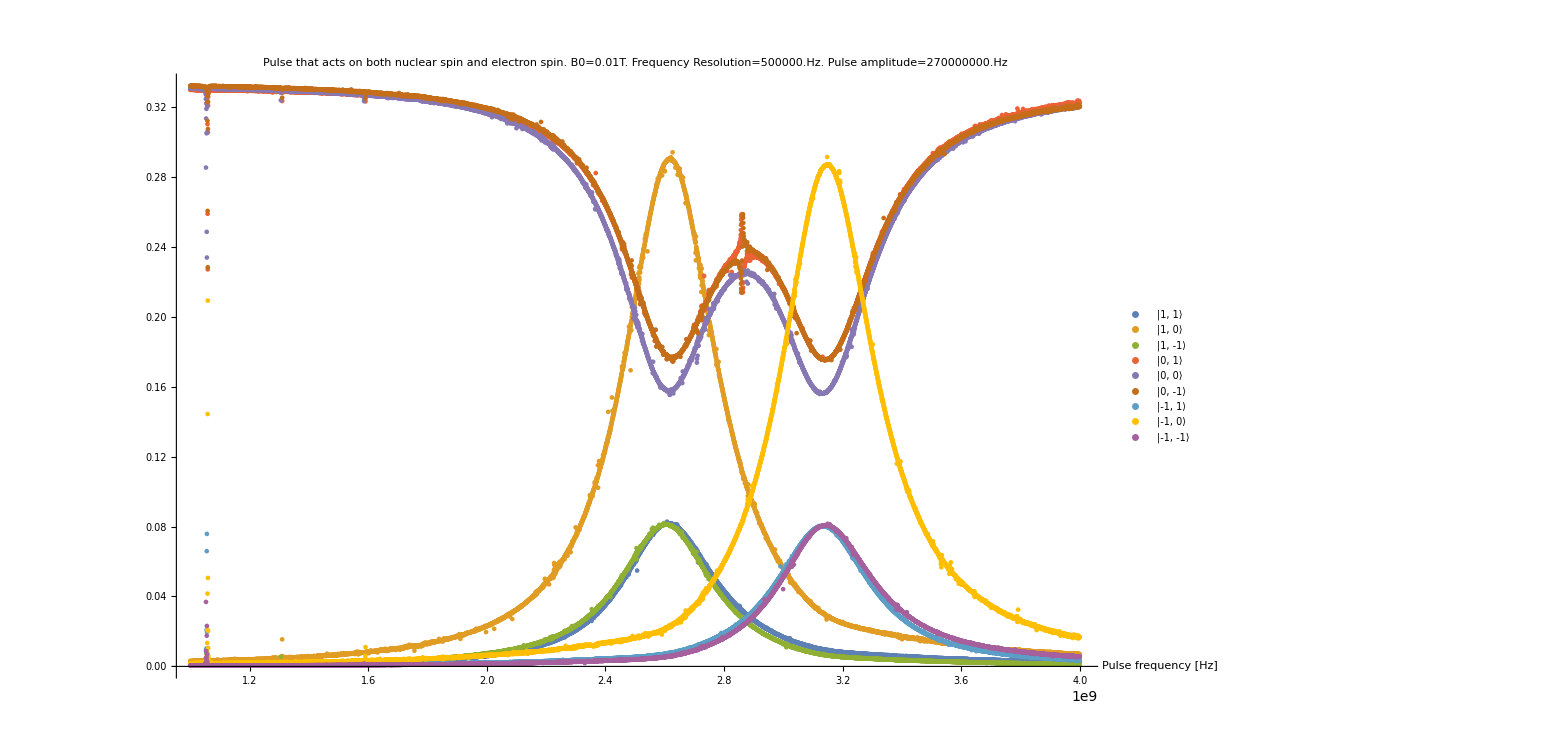
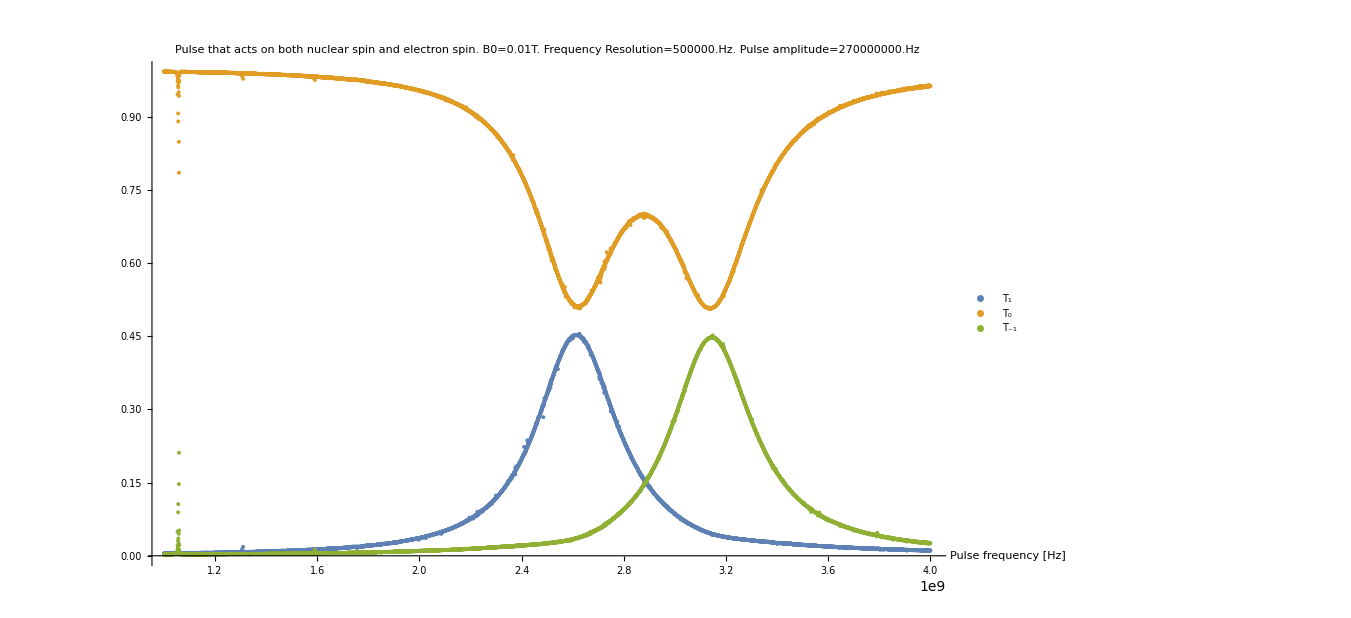
As I thought, this made it possible for all the transitions to ocurr:

-Graphics-

The peaks are too broad for them to be registered on the regular ESR though:

-Graphics-

The solution is probably to lower the pulse amplitude.

I’m not quite sure why there’s a resonance peak at the 1GHz mark... There’s also something going on at 2.86 GHz.

## Run: B0=100G, uniform mixture of T0 states, with a 7 MHz pulse

nv_center_simulation_NO_SPIN_BATH2017-08-23_00.46.27

### Initialisation

#### Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.3*10^9; (* [Hz] *)
pulseFreqEnd =2.9*10^9; (* [Hz] *) 
pulseFreqStep = 0.5*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 7*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 1201

#### Setup Hamiltonian

```mathematica
spins = {1, 1};

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋspinSpin =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋCop =  pulseAmplitude* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1], 2-> SpinMatrixX[1] }, {3, 3} ] ;
ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

#### Energy spectrum of the unperturbed Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV, spins];
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];

eigenStates[0,1] = hamiltonianSpectrum[[1]][[3]][[8]];
eigenStates[0,0] = hamiltonianSpectrum[[1]][[3]][[7]];
eigenStates[0,-1] = hamiltonianSpectrum[[1]][[3]][[9]];

generalState = Sqrt[p1] eigenStates[0,1] + Sqrt[p0] eigenStates[0, 0] + Sqrt[1 - p1-p0] eigenStates[0, -1];
propagator = Outer[Times, generalState, generalState];
density0 = NIntegrate[propagator, {p1, 0, 1}, {p0, 0, 1 - p1}]/NIntegrate[1, {p1, 0, 1}, {p0, 0, 1 - p1}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Results

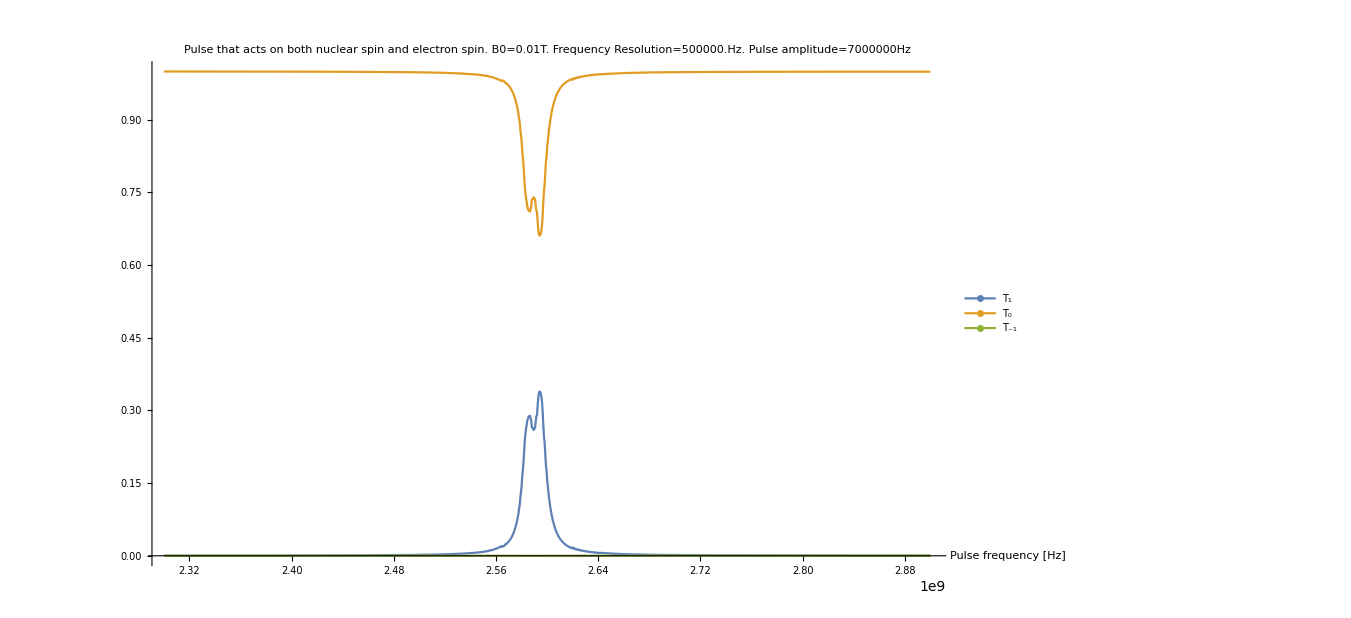
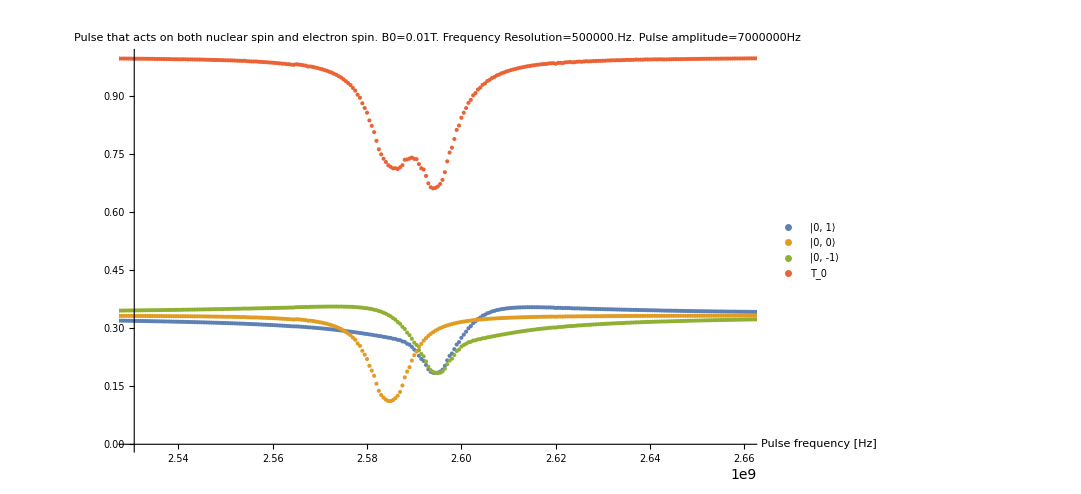
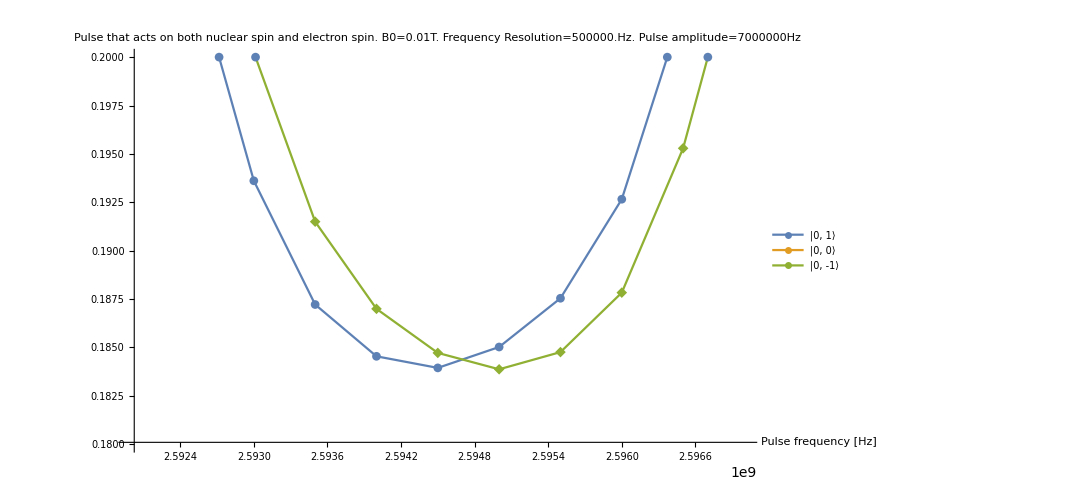
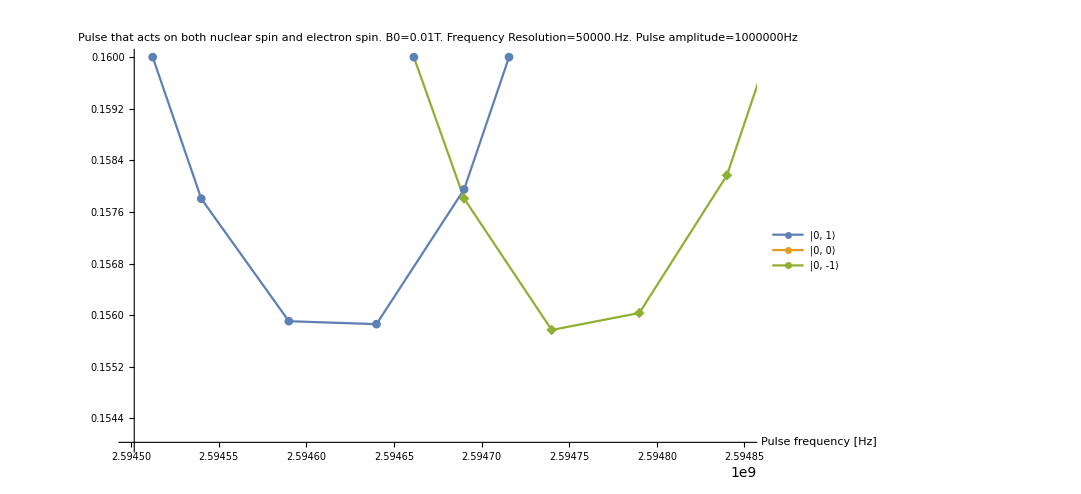
With an amplitude of 7 MHz, zooming into the first of the peaks from the lats simulation, I see two pronounced peaks:

-Graphics-

The three transitions are there but not very visible:

-Graphics-

-Graphics-

The difference in frequency between the two minima of these curves is on the order of 0.5 MHz. Not really sure why the gap is so narrow. In the spectrum the smallest energy difference 2.7 MHz. I guess the uncertainty is 1Mhz for both minima, but that still leaves us short.

{2.75923×10^6,4.38293×10^6,5.53369×10^8,2.82076×10^6,4.26017×10^6,2.58267×10^9,4.91783×10^6,61230.5,-4.98216×10^6}

I’ll run the simulation again over a narrower range, focusing it on these two peaks. I’ll lower the amplitude to 1 MHz as well.

-Graphics-
Peak separation is in the order of 0.1 Hz.
I think I might have to abandon the canonical distribution approach... The transitions between the different states get all mixed up, giving an incorrect ESR.

I’m gonna run it from the pure eigenstates again, 0,1   0,0 and 0,-1.

Try changing the perturbation so that it only acts on the triplet spin. Does changing the phase help at all?

## Wrong perturbation

Turned out the perturbation I used was wrong...

If you have a wave-vector of the form

-Graphics-

the evolution is given by the Schrodinger equation as usual

-Graphics-.

Plugging the former into the latter yields

-Graphics-

So the allowed transitions to only depends on the spectrum of the unperturbed Hamiltonian, and the perturbation itself. The form of the unperturbed Hamiltonian does not come into play. So from this formula, it’s quite clear to see which transitions are allowed, and which aren’t. Our perturbation is of the form

-Graphics-

or

-Graphics-

and this only allows transitions

-Graphics-

which explains why we could never find transitions between states that differed in 1 unit of spin. But now that I look at it again, the perturbation doesn’t even make sense. It’s like an oscillating hyperfine term...

The real perturbation should be:

-Graphics-

Actually, there should be different coefficients in front of each term.

## Run: B0=100G, from |0,0⟩, 100 MHz pulse

Tried to run it with the corrected perturbation. The pulse amplitudes are now

```mathematica
pulseAmplitude = 100*10^6; (* [Hz] *)
pulseAmplitudeE = -pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
```

Not entirely sure if the way I scaled the pulse amplitude on the

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 100*10^6; (* [Hz] *)
pulseAmplitudeE = -pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.3*^9; (* [Hz] *)
pulseFreqEnd =3.2*^9; (* [Hz] *) 
pulseFreqStep = 10*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 91

#### Setup Hamiltonian

```mathematica
spins = {1, 1};
hilbertSubspaceDimensions = 2*spins + 1;

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋspinSpin =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋCop =  (pulseAmplitudeE FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1] }, hilbertSubspaceDimensions ]  + pulseAmplitudeN FullHilbertSpaceOperator[ { 2-> SpinMatrixX[1] }, hilbertSubspaceDimensions ] );
ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

```mathematica
op = KroneckerProduct[Sx, IdentityMatrix[3]];
op = KroneckerProduct[Sx, IdentityMatrix[3]] + KroneckerProduct[IdentityMatrix[3], Sx];
op = ℋCop;

pairs = Select [Flatten[Table[ {i,j}, {i, 1,9}, {j , 1, 9}], 1], op[[ #[[1]], #[[2]] ]] ≠ 0 &];

iToVec[i_] := "|" <> ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[ 1- Mod[i-1, 3]] <> "⟩";

Map[ iToVec[#[[1]]] ↔ iToVec[#[[2]]] &, pairs] // MatrixForm
```

(|1,1⟩↔|1,0⟩
|1,1⟩↔|0,1⟩
|1,0⟩↔|1,1⟩
|1,0⟩↔|1,-1⟩
|1,0⟩↔|0,0⟩
|1,-1⟩↔|1,0⟩
|1,-1⟩↔|0,-1⟩
|0,1⟩↔|1,1⟩
|0,1⟩↔|0,0⟩
|0,1⟩↔|-1,1⟩
|0,0⟩↔|1,0⟩
|0,0⟩↔|0,1⟩
|0,0⟩↔|0,-1⟩
|0,0⟩↔|-1,0⟩
|0,-1⟩↔|1,-1⟩
|0,-1⟩↔|0,0⟩
|0,-1⟩↔|-1,-1⟩
|-1,1⟩↔|0,1⟩
|-1,1⟩↔|-1,0⟩
|-1,0⟩↔|0,0⟩
|-1,0⟩↔|-1,1⟩
|-1,0⟩↔|-1,-1⟩
|-1,-1⟩↔|0,-1⟩
|-1,-1⟩↔|-1,0⟩)

```mathematica
op // MatrixForm
```

(0. | 7762.55 | 0. | -7.07107×10^7 | 0. | 0. | 0. | 0. | 0.
7762.55 | 0. | 7762.55 | 0. | -7.07107×10^7 | 0. | 0. | 0. | 0.
0. | 7762.55 | 0. | 0. | 0. | -7.07107×10^7 | 0. | 0. | 0.
-7.07107×10^7 | 0. | 0. | 0. | 7762.55 | 0. | -7.07107×10^7 | 0. | 0.
0. | -7.07107×10^7 | 0. | 7762.55 | 0. | 7762.55 | 0. | -7.07107×10^7 | 0.
0. | 0. | -7.07107×10^7 | 0. | 7762.55 | 0. | 0. | 0. | -7.07107×10^7
0. | 0. | 0. | -7.07107×10^7 | 0. | 0. | 0. | 7762.55 | 0.
0. | 0. | 0. | 0. | -7.07107×10^7 | 0. | 7762.55 | 0. | 7762.55
0. | 0. | 0. | 0. | 0. | -7.07107×10^7 | 0. | 7762.55 | 0.)

#### Energy spectrum of the unperturbed Hamiltonian

In terms of the eigenstates of the Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV, spins]; 
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

```mathematica
hamiltonianSpectrum[[1]][[1]]
```

{3.15026×10^9,3.1475×10^9,3.14312×10^9,2.58975×10^9,2.58692×10^9,2.58266×10^9,-3105.84,-4.92093×10^6,-4.98216×10^6}

```mathematica
{3.1502573369663377*^9,3.1474981066489053*^9,3.1431151730484695*^9,2.5897457603508644*^9,2.586924999188904*^9,2.5826648269515305*^9,-3105.8378033638,-4.920933399331093*^6,-4.9821639178676605*^6} - 
{3.1474981066489053*^9,3.1431151730484695*^9,2.5897457603508644*^9,2.586924999188904*^9,2.5826648269515305*^9,-3105.8378033638,-4.920933399331093*^6,-4.9821639178676605*^6, 0}
```

{2.75923×10^6,4.38293×10^6,5.53369×10^8,2.82076×10^6,4.26017×10^6,2.58267×10^9,4.91783×10^6,61230.5,-4.98216×10^6}

In terms of eigenstates of the spin triplet and nuclear spin

```mathematica
hamiltonianSpectrumPure = NVCenterEnergySpectrum2[ℋ[0,0], spins];
hamiltonianSpectrumPure[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | |-1,0⟩ | -1
3.1475×10^9 | |-1,1⟩ | 0
3.14312×10^9 | |-1,-1⟩ | -2
2.58974×10^9 | |1,0⟩ | 1
2.58692×10^9 | |1,-1⟩ | 0
2.58266×10^9 | |1,1⟩ | 2
0. | |0,0⟩ | 0
-4.91923×10^6 | |0,1⟩ | 1
-4.98077×10^6 | |0,-1⟩ | -1)

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];

eigenStates[0,1] = hamiltonianSpectrum[[1]][[3]][[8]];
eigenStates[0,0] = hamiltonianSpectrum[[1]][[3]][[7]];
eigenStates[0,-1] = hamiltonianSpectrum[[1]][[3]][[9]];

generalState = Sqrt[p1] eigenStates[0,1] + Sqrt[p0] eigenStates[0, 0] + Sqrt[1 - p1-p0] eigenStates[0, -1];
propagator = Outer[Times, generalState, generalState];
density0 = NIntegrate[propagator, {p1, 0, 1}, {p0, 0, 1 - p1}]/NIntegrate[1, {p1, 0, 1}, {p0, 0, 1 - p1}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
initialState = IdentityMatrix[9][[6]] (* 0,-1 *)
initialState = IdentityMatrix[9][[4]] (* 0,1 *)
initialState = IdentityMatrix[9][[5]] (* 0,0 *)

density0 = Outer[Times, initialState, initialState];
```

{0,0,0,0,0,1,0,0,0}

{0,0,0,1,0,0,0,0,0}

{0,0,0,0,1,0,0,0,0}

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

## Todo:

Todo
- Create wavefunction version of the simulation
- Create the canonical initial state.
- Clean up and fix the 9-state version
	- Make the function parameterse be passed through rules
	- Add Plot to RunSimulation function arguments
	- Make RunSimulation add to a given list, instead of returning a list
	- Dephasing
- Try the Rabi oscillation function
- Write documentation
- Prepare a report for prof








Todo for next time:

- Check that the Hamiltonian is correct again.
- Run the whole simulation again, with a smaller magnetic field, but with larger pulseAmplitude and pulse length.
- Add some features:
	- Currently it plots the subsystem states, but it might be useful if it could plot all the 9 states of the system.
	- Enable truncated spin matrices

	- Make the freqStep dependent on the gradient of the curve. Instead of freqStep you could specify, number of 	datapoints per unit length on graph curve
			- Oort , make the evolution time dependent on the gradient of the curve.
	- Function that returns a Rabi oscillation at a certain frequency
	- Dephasing

Make RunSimulation add to a given list, instead of returning a list

Finish documentation



1. Make some good results of
- B0 = 0
- B0 = /= 0
- Add a spin or two with B0 = /= 0

2. Dephasing

3. Create some tasks for the next guy
- Make freqStep dependent on the gradient of the curve
- Make tEnd dependent on the gradient of the curve

4. Finish documentation.
- Mention what truncated spin matrices are